```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./mub0/buffer/mSigma.dat"]];
T0=Flatten[Import["./mub0/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub0linear=Transpose[{T0[[2;;Length[t]-2]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
fpi=Flatten[Import["./mub300/buffer/mSigma.dat"]];
T300=Flatten[Import["./mub300/buffer/TMeV.dat"]];
t=-(T300-T300[[1]])/T300[[1]];
datamub300=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub300=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];
b1mub300linear=Transpose[{T300[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T300]-2}]]}];

fpi=Flatten[Import["./mub400/buffer/mSigma.dat"]];
T400=Flatten[Import["./mub400/buffer/TMeV.dat"]];
t=-(T400-T400[[1]])/T400[[1]];
datamub400=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub400=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];
b1mub400linear=Transpose[{T400[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T400]-2}]]}];

fpi=Flatten[Import["./mub500/buffer/mSigma.dat"]];
T500=Flatten[Import["./mub500/buffer/TMeV.dat"]];
t=-(T500-T500[[1]])/T500[[1]];
datamub500=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub500=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];
b1mub500linear=Transpose[{T500[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T500]-2}]]}];

fpi=Flatten[Import["./mub550/buffer/mSigma.dat"]];
T550=Flatten[Import["./mub550/buffer/TMeV.dat"]];
t=-(T550-T550[[1]])/T550[[1]];
datamub550=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub550=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub550[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T550]-2}]]}];
b1mub550linear=Transpose[{T550[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub550[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T550]-2}]]}];

fpi=Flatten[Import["./mub575/buffer/mSigma.dat"]];
T575=Flatten[Import["./mub575/buffer/TMeV.dat"]];
t=-(T575-T575[[1]])/T575[[1]];
datamub575=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub575=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub575[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T575]-2}]]}];
b1mub575linear=Transpose[{T575[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub575[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T575]-2}]]}];

fpi=Flatten[Import["./mub600/buffer/mSigma.dat"]];
T600=Flatten[Import["./mub600/buffer/TMeV.dat"]];
t=-(T600-T600[[1]])/T600[[1]];
datamub600=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub600=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];
b1mub600linear=Transpose[{T600[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];
```

## Plot

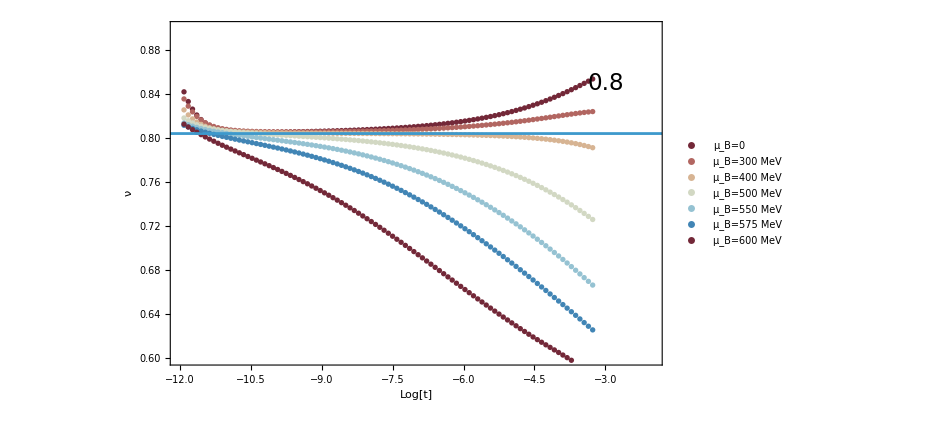

```mathematica
plotT=Show[ListPlot[{b1mub0,b1mub300,b1mub400,b1mub500,b1mub550,b1mub575,b1mub600},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.18}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=300 MeV","μ_B=400 MeV","μ_B=500 MeV","μ_B=550 MeV","μ_B=575 MeV","μ_B=600 MeV"},LabelStyle->16],{0.23,0.32}],
PlotRange->{{-12,-2},{0.6,0.9}},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.8043},{10,0.8043}}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-3,0.85}]}]
```

```mathematica
(*Export["./Tscaling.pdf",plotT]*)
```

```mathematica
Export["./LOdata/mub0.dat",b1mub0];
Export["./LOdata/mub300.dat",b1mub300];
Export["./LOdata/mub400.dat",b1mub400];
Export["./LOdata/mub500.dat",b1mub500];
Export["./LOdata/mub550.dat",b1mub550];
Export["./LOdata/mub575.dat",b1mub575];
Export["./LOdata/mub600.dat",b1mub600];
```